## exp(-β ζ)

```mathematica
zG[x_, μ_]=μ Sin[x]/x;
zz[x_,μ_,β_]=-1/β Log[1-β zG[x,μ]];
```

```mathematica
CompactionC[x_,μ_,β_]=2/3(1-(1+x D[zz[x,μ,β], x])^2)//Simplify;
```

```mathematica
rmcond[x_,mb_]=(D[zz[x,μ,mb/μ], x]+x D[D[zz[x,μ,mb/μ], x], x])/μ//Simplify
```

(mb x+Sin[x]-x^2 Sin[x]-Cos[x] (x+mb Sin[x]))/(x-mb Sin[x])^2

```mathematica
rmcondapprox[x_,ϵ_]=Normal[Series[rmcond[x,1-ϵ],{ϵ,0,1},{x,0,2}]]
```

x/5+(-24/x^3+(59 x)/350) ϵ

```mathematica
rmapprox[ϵ_]=x/.Solve[rmcondapprox[x,ϵ]==0,x][[4]]
```

(2 √5 21^(1/4) ϵ^(1/4))/(70+59 ϵ)^(1/4)

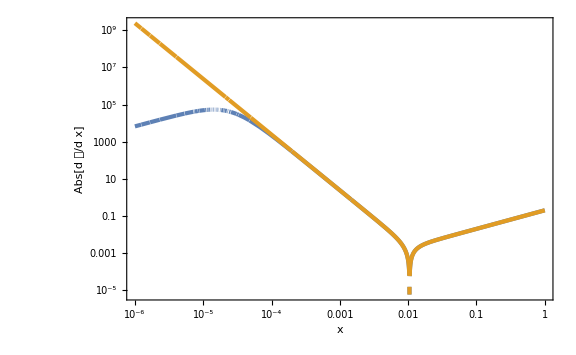

```mathematica
LogLogPlot[{Abs[rmcond[x,1-10^-10]],Abs[rmcondapprox[x,10^-10]]},{x,10^-6,1},WorkingPrecision->30,GridLines->{{rmapprox[10^-10]},None},FrameLabel->{x,Abs[Row[{"d"𝒞,"/","d"x}]]}]
```

```mathematica
Cmapprox[β_]=Normal[Series[CompactionC[rmapprox[ϵ],(1-ϵ)/β,β],{ϵ,0,0}]]
```

(8 (-1+β))/(3 β^2)

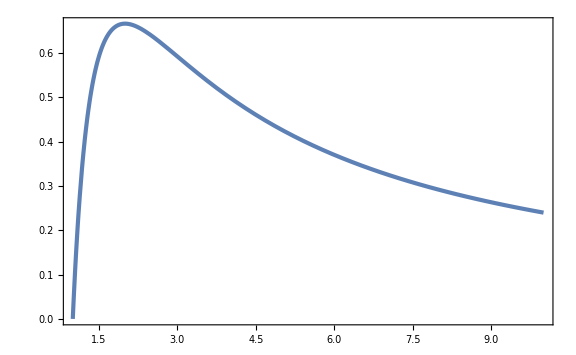

```mathematica
Plot[Cmapprox[β],{β,1,10}]
```

```mathematica
arealR[x_,μ_,β_]=Exp[zz[x,μ,β]]x;
Rp[x_,μ_,β_]=D[arealR[x,μ,β], x]//Simplify;
```

```mathematica
intapprox[x_,β_]=Normal[Series[CompactionC[x,(1-ϵ)/β,β] arealR[x,(1-ϵ)/β,β]^2 Rp[x,(1-ϵ)/β,β],{ϵ,0,0},{x,0,2}]]//Simplify
```

(3^(-1+3/β) 8^(1+1/β) (x^2)^((-3+β)/β) (-2+β) (-1+β))/β^3

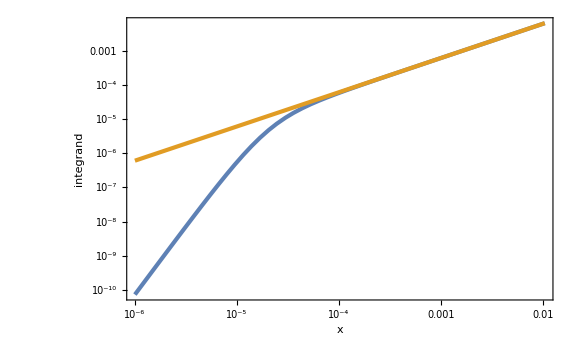

```mathematica
LogLogPlot[{CompactionC[x,(1-ϵc)/βc,βc] arealR[x,(1-ϵc)/βc,βc]^2 Rp[x,(1-ϵc)/βc,βc],intapprox[x,βc]},{x,10^-6,rmapprox[10^-10]},WorkingPrecision->30,FrameLabel->{x,"integrand"}]
```

```mathematica
Cbarapprox[β_]=Normal[Series[3Integrate[intapprox[x,β],{x,0,rmapprox[ϵ]}]/arealR[rmapprox[ϵ],(1-ϵ)/β,β]^3,{ϵ,0,0}]]//Simplify
```

(8 (-1+β))/(3 β^2)

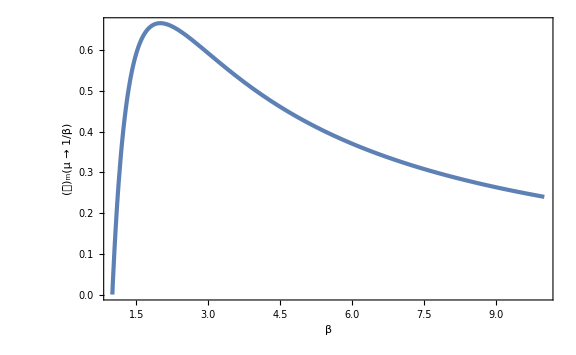

```mathematica
Plot[Cbarapprox[β],{β,1,10},GridLines->{None,{2/5}},FrameLabel->{β,Subscript[OverBar[𝒞], "m"]["μ → 1/β"]}]
```

### β = 6, ϵ = 10^-10

```mathematica
βc=6;
ϵc=10^-10;
μc=(1-ϵc)/βc;
```

```mathematica
rm=x/.FindRoot[rmcond[x,1-ϵc]==0,{x,10^-3},WorkingPrecision->30]
```

0.010466321365916058593334508227

```mathematica
3NIntegrate[CompactionC[x,μc,βc] arealR[x,μc,βc]^2 Rp[x,μc,βc],{x,0,rm}]/arealR[rm,μc,βc]^3
```

0.37035

```mathematica
Cbarapprox[βc]//N
```

0.37037

## exp(-Λ ζ^p)

```mathematica
Integrate[Exp[-Λ zp^p]/.{Λ->1,p->3/10},{zp,0,z}]//FullSimplify
```

Gamma[13/3]-10/3 Gamma[10/3,z^(3/10)]

```mathematica
zg[z_]=Gamma[10/3](10/3-10/3 GammaRegularized[10/3,z^(3/10)]);
```

```mathematica
zg[z]-Integrate[Exp[-Λ zp^p]/.{Λ->1,p->3/10},{zp,0,z}]//FullSimplify
```

0

```mathematica
FullSimplify[Normal[Series[zg[z],{z,0,2}]],{z>0}]
```

z-(10 z^(13/10))/13+(5 z^(8/5))/16-(5 z^(19/10))/57

```mathematica
zz[g_]=InverseGammaRegularized[10/3,3/10(10/3-g/Gamma[10/3])]^(10/3)
```

InverseGammaRegularized[10/3,3/10 (10/3-g/Gamma[10/3])]^(10/3)

```mathematica
FullSimplify[zg[zz[g]],{g>0,g<Gamma[13/3]}]
```

g

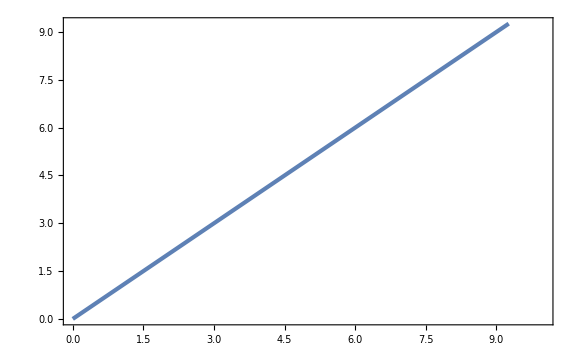

```mathematica
Plot[zg[zz[g]],{g,0,10}]
```

```mathematica
zhat[x_,μ2_]=zz[μ2 Sin[x]/x]
```

InverseGammaRegularized[10/3,3/10 (10/3-(μ2 Sin[x])/(x Gamma[10/3]))]^(10/3)

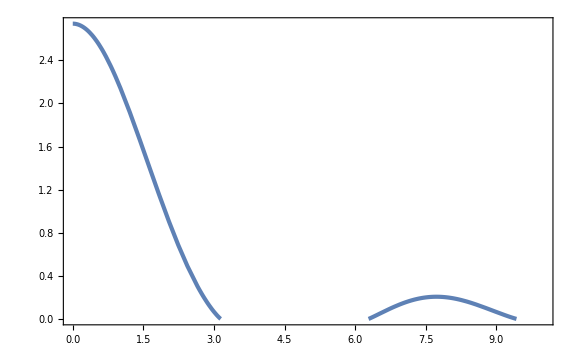

```mathematica
Plot[zhat[x,1],{x,0,10},PlotRange->Full]
```

## (Λ-ζ)^-n

```mathematica
zg[z_,n_,Λ_]=Collect[Integrate[Λ^n(Λ-zp)^-n,{zp,0,z},Assumptions->{n<1,Λ>0,Λ>z>0}],z+Λ,Simplify]
```

(-Λ+Λ^n (-z+Λ)^(1-n))/(-1+n)

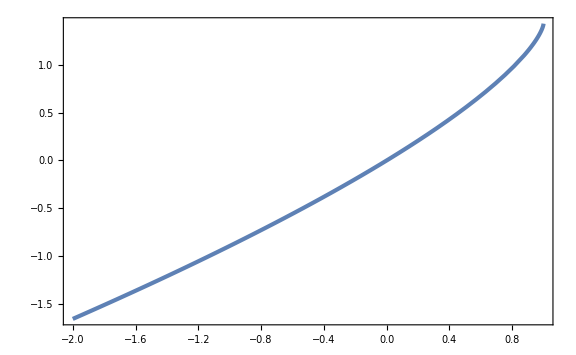

```mathematica
Plot[zg[z,3/10,1],{z,-2,1}]
```

```mathematica
zg[-10^-2,3/10,1]//Simplify
```

10/7-101^(7/10)/(7 10^(2/5))

```mathematica
Simplify[Normal[Series[zg[z,n,Λ],{z,0,2}]],{Λ>0}]
```

z+(n z^2)/(2 Λ)

```mathematica
Pz[z_,n_,Λ_,σ2_]=1/Sqrt[2π σ2] Exp[-zg[z,n,Λ]^2]D[zg[z,n,Λ], z]//Simplify
```

(ⅇ^(-((Λ-Λ^n (-z+Λ)^(1-n))^2)/(-1+n)^2) Λ^n (-z+Λ)^-n)/(√(2 π) √σ2)

```mathematica
NIntegrate[Pz[z,3/10,1,10^-2]z,{z,-∞,1},WorkingPrecision->30]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {-282.755763942463547141114768234}. NIntegrate obtained -5.53973416178569722857044655574×10^25623911+1.0013565308150833051585286869×10^25623912 ⅈ and -5.53973416178569722857044655574×10^25623911+1.0013565308150833051585286869×10^25623912 ⅈ for the integral and error estimates.

-5.5397341617856972285704465557×10^25623911+1.0013565308150833051585286869×10^25623912 ⅈ

```mathematica
Normal[Series[Pz[z,2,Λ,σ2],{z,Λ,2}]]
```

(ⅇ^(-Λ^2-(2 Λ^3)/(z-Λ)-Λ^4/(z-Λ)^2) Λ^2)/(√(2 π) (z-Λ)^2 √σ2)

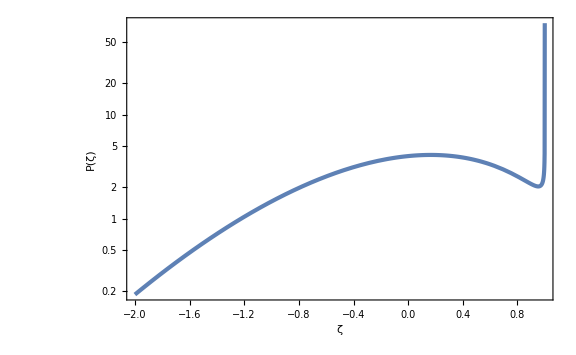

```mathematica
LogPlot[Pz[z,3/10,1,10^-2],{z,-2,1},FrameLabel->{{P[ζ],None},{ζ,Row[{n==2,", ",Λ==-1}]}}]
```

```mathematica
zeta[g_,n_,Λ_]=Simplify[InverseFunction[zg[#,n,Λ]&][g],{Λ>0,n<1}]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

Λ-(Λ^-n (g (-1+n)+Λ))^(1/(1-n))

```mathematica
FullSimplify[zg[zeta[g,n,Λ],n,Λ],{n<1,Λ>0,g<Λ/(n-1)}]
```

g

## (ζ+Λ)^-n

```mathematica
zg[z_,n_,Λ_]=Collect[Integrate[Λ^n(zp+Λ)^-n,{zp,0,z},Assumptions->{Λ>0,z>0}],z+Λ,Simplify]
```

Λ/(-1+n)-(Λ^n (z+Λ)^(1-n))/(-1+n)

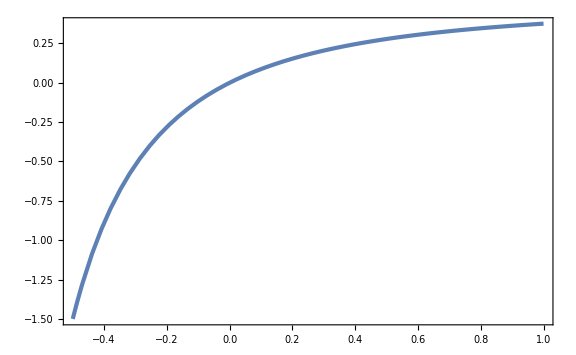

```mathematica
Plot[zg[z,3,1],{z,-1/2,1}]
```

```mathematica
zg[-10^-2,3,1]//Simplify
```

-199/19602

```mathematica
Simplify[Normal[Series[zg[z,n,Λ],{z,0,2}]],{Λ>0}]
```

z-(n z^2)/(2 Λ)

```mathematica
Pz[z_,n_,Λ_,σ2_]=1/Sqrt[2π σ2] Exp[-zg[z,n,Λ]^2]D[zg[z,n,Λ], z]//Simplify
```

(ⅇ^(-((Λ-Λ^n (z+Λ)^(1-n))^2)/(-1+n)^2) Λ^n (z+Λ)^-n)/(√(2 π) √σ2)

```mathematica
NIntegrate[Pz[z,4,1,10^-2]z,{z,-1,∞},WorkingPrecision->30]
```

-0.25281249936751743466067589971

```mathematica
Normal[Series[Pz[z,2,Λ,σ2],{z,Λ,2}]]
```

(ⅇ^(-Λ^2/4))/(4 √(2 π) √σ2)-(ⅇ^(-Λ^2/4) (z-Λ) (4+Λ^2))/(16 √(2 π) Λ √σ2)+(ⅇ^(-Λ^2/4) (z-Λ)^2 (24+10 Λ^2+Λ^4))/(128 √(2 π) Λ^2 √σ2)

General::munfl: Exp[-2.09702×10^24] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.09604×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-32743.4] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

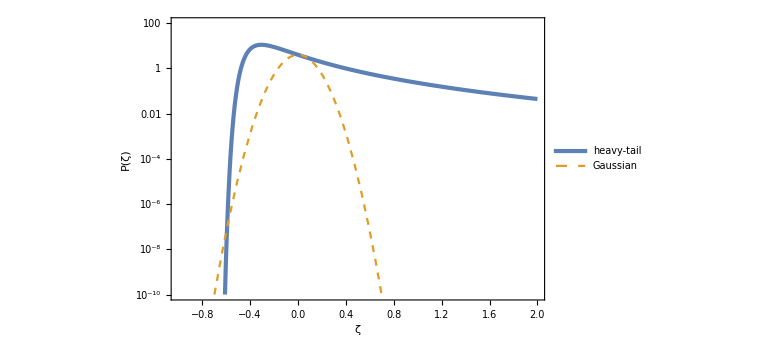

```mathematica
ns=4;
Λs=10^0;
LogPlot[{Pz[z,ns,Λs,10^-2],1/Sqrt[2π 10^-2] Exp[-z^2/(2 10^-2)]},{z,-Λs,2},FrameLabel->{{P[ζ],None},{ζ,Row[{n==ns,", ",Λ==1}]}},PlotRange->{10^-10,10^2},PlotStyle->{AbsoluteThickness[3],Dashed},PlotLegends->Placed[LineLegend[{"heavy-tail","Gaussian"},LabelStyle->Directive[Black,Larger,FontFamily->"Palatino"]],{0.8,0.2}]]
```

```mathematica
zeta[g_,n_,Λ_]=Simplify[InverseFunction[zg[#,n,Λ]&][g],{Λ>0,n>2}]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

-Λ+(Λ^-n (g-g n+Λ))^(1/(1-n))

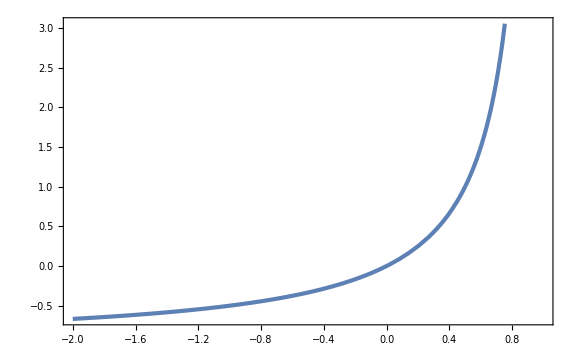

```mathematica
Plot[zeta[g,2,1],{g,-2,1}]
```

```mathematica
FullSimplify[zg[zeta[g,n,Λ],n,Λ],{n>2,Λ>0,g<Λ/(n-1)}]
```

g